```mathematica
(*MIGUEL ANGEL NAVARRO ARENAS
Actividades propuestas
Diseñe un módulo Mathematica que,tomando como entrada los siguientes
parámetros,nos proporcione como salida la simulación del AC unidimensional
correspondiente
Inicial:Lista con la configuración inicial del AC
Regla:Valor entero que codifica la regla como un número de Wolfram
t:Número de configuraciones a calcular a partir de la configuración inicial
AC[Inicial_List,Regla_Integer,t_Integer]:=Module[{},…]
Considere un conjunto de estados binario {0,1} y condición de frontera periódica.Se recomienda implementar módulos para cada acción significativa de la simulación
(por ejemplo,un módulo que convierta el número de regla en una lista de listas,otro módulo que,a partir de una configuración calcule la siguiente,etc.)
*)
ListFromRule [rule_Integer, numVecinos_Integer: 3]:= Module[{listaIni, divisor,reversa, i,j,soluc},
listaIni = {{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1}};
divisor=rule;
i = 1;
While[divisor > 2, 
If[Mod[divisor,2]==0,
AppendTo[listaIni[[i]], 0];
divisor = divisor/2;,
AppendTo[listaIni[[i]],1];
divisor=(divisor-1)/2;]
i++;
]
If[divisor==2,AppendTo[listaIni[[i]], 0];,AppendTo[listaIni[[i]], 1];]
For[j=Length[listaIni], j>=1, j--,
If[Length[listaIni[[j]]]==3, AppendTo[listaIni[[j]],0];]
];
Return[listaIni];
]
```

```mathematica
ListFromRule[100]
```

{{0,0,0,0},{0,0,1,0},{0,1,0,1},{0,1,1,0},{1,0,0,0},{1,0,1,1},{1,1,0,1},{1,1,1,0}}

```mathematica
Transition[rule_Integer,state_]:=Module[{res,list,ini,i,case,fin},
res={};
list = ListFromRule[rule];
ini=Flatten[ Cases[list,{state[[Length[state]]],state[[1]],state[[2]],_}]];
AppendTo[res,ini[[4]]];
For[i=2,i<Length[state], i++,
case=Flatten[Cases[list,{state[[i-1]],state[[i]],state[[i+1]],_}]];

AppendTo[res,case[[4]]];
];
fin=Flatten[Cases[list,{state[[Length[state]-1]],state[[Length[state]]],state[[1]],_}]];
AppendTo[res,fin[[4]]];
Return[res];
]
```

```mathematica
Transition[23,{1,0,1,0,1,0,1,0,1}]
```

{0,0,1,0,1,0,1,0,0}

```mathematica
AutomataCelular[state_,rule_Integer,transitions_Integer]:=Module[{res,i,sigEstado},
res={state};
sigEstado=state;
For[i=0, i<transitions, i++,
sigEstado = Transition[rule,sigEstado];
AppendTo[res,sigEstado];
];
ArrayPlot[res]
]
```

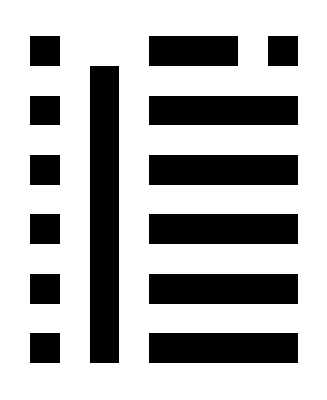

```mathematica
AutomataCelular[{1,0,0,0,1,1,1,0,1},69,10]
```